```mathematica
(*电位的差分计算*)
```

```mathematica
(∂^2 V(x,y))/(∂x^2)+(∂^2 V(x,y))/(∂y^2)=0
Subscript[V, 0]≈1/4 (Subscript[V, 1]+Subscript[V, 2]+Subscript[V, 3]+Subscript[V, 4])
```

```mathematica
(*聚焦电极内的电位计算*)
```

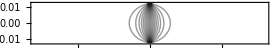

```mathematica
V0=1.0;b=5*10^-3;c=25*10^-3;a=5c;
m=5;h=b/m;k=a/h;n=c/h;
col=2k+m+1;row=n+1;
(*initial values*)
V=Table[V0/(col-1)*(j-1.),{i,row},{j,col}];
Do[V[[1,j]]=V[[row,j]]=V0/m*(j-k-1.),{j,k+2,k+m+1}];
Do[V[[1,j]]=V[[row,j]]=0.,{j,k+1}];
Do[V[[1,j]]=V[[row,j]]=V0,{j,k+m+2,col}];
(*iteration*)
temp=V;
Do[Do[temp[[i,j]]=(V[[i,j-1]]+V[[i,j+1]]+V[[i-1,j]]+V[[i+1,j]])/4,{i,2,row-1},{j,2,col-1}];V=temp,{p,800}]
(*interpolation*)
temp={};
Do[x=(j-(col+1)/2.)*h;y=((row+1)/2.-i)*h;AppendTo[temp,{{x,y},V[[i,j]]}],{i,row},{j,col}]
V=Interpolation[temp];
V>>"e:/potential";
(*Contours*)
ContourPlot[V[x,y],{x,-(col-1)/2*h,(col-1)/2*h},{y,-(row-1)/2*h,(row-1)/2*h},ContourShading->False,AspectRatio->0.1,PlotPoints->200,Axes->True,Contours->0.05Range[19]]
```

```mathematica
Clear[V0,b,c,a,m,h,k,n,col,row,V,temp,x,y]
```

InterpolatingFunction[{{-0.1275,0.1275},{-0.0125,0.0125}},<>]

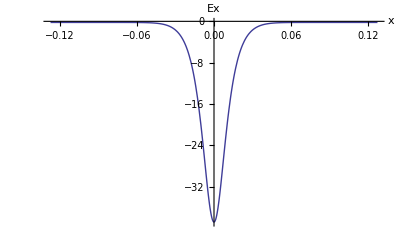

```mathematica
<<"e:/potential";
V=%
V0=1.0;b=5*10^-3;c=25*10^-3;a=5c;
m=5;h=b/m;k=a/h;n=c/h;
col=2k+m+1;row=n+1;
Ex[x_]:=Evaluate[-D[V[x,y],x]/.y->0];
Plot[Ex[x],{x,-(col-1)/2*h,(col-1)/2*h},PlotRange->All,AxesLabel->{"x","Ex"}]
```

```mathematica
Clear[V0,b,c,a,m,h,k,n,col,row,V,x,y,Ex,Ey,eqs,figure,s,g]
```

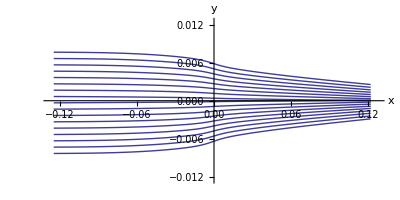

```mathematica
<<"e:/potential";
V=%;V0=1.0;b=5*10^-3;c=25*10^-3;a=5c;
m=5;h=b/m;k=a/h;n=c/h;
col=2k+m+1;row=n+1;specificcharge=-1.75631*10^11;
Ex[x_,y_]:=-D[V[x,y],x];
Ey[x_,y_]:=-D[V[x,y],y];
eqs={x''[t]==specificcharge*Ex[x[t],y[t]],
y''[t]==specificcharge*Ey[x[t],y[t]],
x[0]==-a,x'[0]==10^6,y[0]==ystart,y'[0]==Sign[ystart]*10^3};
figure={};
Do[s=NDSolve[eqs,{x,y},{t,0,2.3*10^-7}];
{x,y}={x,y}/.s[[1]];
g=ParametricPlot[{x[t],y[t]},{t,0,2.3*10^-7},PlotRange->{{-(col-1)/2*h,(col-1)/2*h},{-(row-1)/2*h,(row-1)/2*h}}];
AppendTo[figure,g];Clear[x,y],{ystart,-c/3,c/3,10^-3}]
Show[figure,AxesLabel->{"x","y"},AspectRatio->0.5]
```